#### Import data

```mathematica
(* import the data sheet *)
all=Import[NotebookDirectory[]<>"LOUPE_Graph-based_AllSamples.csv"];
L=Length[all];
Print["Cells in the entire data set:"]
L-1
(* 
this data is 2 time L,
the number of lines, L-1, is equal to the total number of cells kept by LOUPE browser (where samples are calle "Library ID") after cellranger_aggr normalized the data,
the data does not contain genes any more,
the 1. column contains information about the BARCODE and the sample in which that barcode was found followed by -x, where x is the sample ID, e.g. GATTACCA-x, x=1,2,3,4,5,6, 
*)
(* 
this loop extracts the   
*)
sub={}&/@Range[1,6,1];
AppendTo[
sub⟦
ToExpression[StringTake[all⟦#,1⟧,-1]]
⟧
,all⟦#⟧
]&/@Range[2,L,1];
Print["Cells in each sample (027pre, 035pre, 027post, 035post, h1, h2):"]
sizes=Length[sub⟦#⟧]&/@Range[1,sub//Length,1]

(* this is literally a checksum *)
Print["Checksum:"]
Total[sizes]
(* 
this function f[];
takes a fixed numner of clusters (23), and an element of the data table sub⟦⟧;
calculates the number of cells within sub⟦⟧ that are found to be in each cluster;
returns a 3D data field with total number of cells per cluster for that sample (1st), and the fraction of cells (2nd, normalized to tootal cell count in the sample),
and the total number of cells again, as a control (3rd);
here, "sample" can also be replaced by a bundle of samples
*)

f[a_]:=Module[
{p1,l1,p2,l2,clusterCount,q1,q2,AD,CVM,KS,WUS,WSR},
l1=Length[a];
clusterCount=23;
p1=0&/@Range[1,clusterCount,1];
Table[
If[a⟦l,2⟧=="Cluster "<>ToString[#],p1⟦#⟧++]&/@Range[1,clusterCount,1];
,{l,1,l1}];
{p1,p1/Total[p1]//N,Total[p1]}
](* END of MODULE *)
(*
sample IDs and cell counts are:
1 : AML027-pre, 3831 cells
2 : AML035-pre, 1904 cells
3 : AML027-post, 3340 cells
4 : AML035-post, 750 cells
5 : helathy1, 1811 cells
6 : helathy2, 2242 cells
*)
(* Re-arranging to healhy1, healthy2, post027, post035, pre027, pre035*)
Q=(f[sub⟦#⟧]⟦2⟧)&/@Range[1,6,1];
(* this generates the data pooled by conditions. Pooling occurs post aggregation and clustering, but pre diversity calculations *)
Qsum={
f[Join[sub⟦6⟧,sub⟦5⟧]]⟦2⟧,(* healthy *)
f[Join[sub⟦1⟧,sub⟦2⟧]]⟦2⟧,(* pre *)
f[Join[sub⟦3⟧,sub⟦4⟧]]⟦2⟧(* post *)
};
```

Cells in the entire data set:

13878

Cells in each sample (027pre, 035pre, 027post, 035post, h1, h2):

{3831,1904,3340,750,1811,2242}

Checksum:

13878

#### pooled conditions: healthy vs pre vs post

23.

{{0.374537,0.0555144,0.0143104,0.,0.0439181,0.00197385,0.0895633,0.,0.035776,0.00370096,0.11547,0.,0.000246731,0.0994325,0.000246731,0.,0.0471256,0.0661239,0.,0.00814212,0.0439181,0.,0.},{0.00784656,0.129904,0.109329,0.155013,0.0816042,0.0945074,0.0666085,0.,0.0786399,0.00087184,0.0104621,0.0836966,0.,0.00592851,0.,0.0692241,0.0322581,0.0120314,0.000174368,0.0458588,0.0158675,0.000174368,0.}}

{0.695652,0.826087}

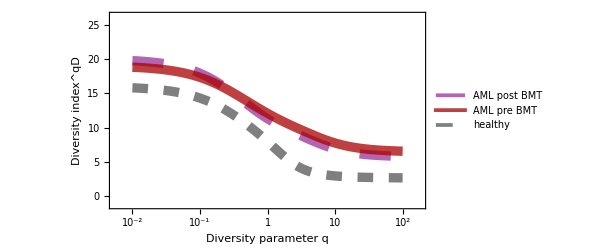

/Users/altrock/Dropbox/Projects_Dropbox/scRNAseq_Diversity/analysis/GraphBasedClustering_analysis/qDplot.pdf

```mathematica
qD[p_,q_]:=If[
q==1,Exp[-Sum[If[p⟦i⟧==0,0,p⟦i⟧Log[p⟦i⟧]],{i,1,p//Length}]]
,(Sum[p⟦i⟧^q,{i,1,p//Length}])^(1/(1-q))
];
n=Qsum⟦2⟧//Length//N
{Qsum⟦1⟧,Qsum⟦2⟧}
{qD[Qsum⟦1⟧,10^-12]/n,qD[Qsum⟦2⟧,10^-12]/n}

qDplot=Plot[{
qD[Qsum⟦3⟧,10^x],qD[Qsum⟦2⟧,10^x],qD[Qsum⟦1⟧,10^x]
},{x,-2,2}
,PlotRange->{{-2.25,2.25},25{-0.05,1.05}}
,Frame->True
,Axes->False
,AspectRatio->0.55
,ImageSize->450
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
, FrameLabel -> {{"Diversity index^qD",None},{"Diversity parameter q",None}}
,FrameTicks->{
{{{0,"0"},{5,"5"},{25,"25"},{10,"10"},{15,"15"},{20,"20"}},None},
{{{-2,"10^-2"},{-1,"10^-1"},{0,"1"},{1,"10"},{2,"10^2"}},None}
}
,PlotStyle->{
Directive[Dashing[{0.05,0.05}],Thickness[0.015],Opacity[0.6,Purple]]
,Directive[Thickness[0.015],Opacity[0.75,Darker[Red]]]
,Directive[Dashing[{0.025,0.025}],Thickness[0.015],Opacity[0.5,Black]]
}
,PlotLegends->Placed[{"AML post BMT","AML pre BMT","healthy"},{0.725,0.75}]
]

Export[NotebookDirectory[]<>"qDplot.pdf",qDplot,"PDF"]
```